```mathematica
p={{0,0},{2,0},{1,1},{2,2},{0,2},{1,1},{3/8,1/8},{1,1/8},{9/8,1/8},{3/8,1/4},{1,1/4},{9/8,1/16}}
```

{{0,0},{2,0},{1,1},{2,2},{0,2},{1,1},{3/8,1/8},{1,1/8},{9/8,1/8},{3/8,1/4},{1,1/4},{9/8,1/16}}

```mathematica
p0=Polygon[{p[[1]],p[[2]],p[[3]],p[[4]],p[[5]],p[[6]]}]
```

Polygon[…]

```mathematica
p1=Polygon[{p[[7]],p[[10]],p[[11]],p[[8]],p[[9]],p[[12]],p[[8]]}]
```

Polygon[…]

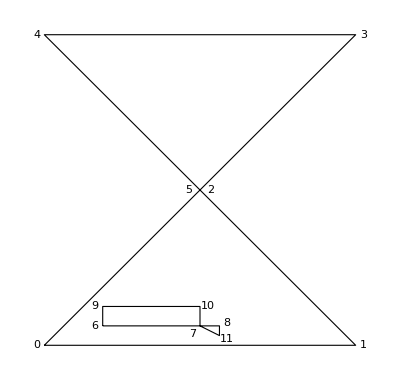

```mathematica
Show[
Graphics[{EdgeForm[Black],FaceForm[White],p0}],
Graphics[{EdgeForm[Black],FaceForm[White],p1}],
Graphics[Text["0",p[[1]]+{-0.05,0.0}]],
Graphics[Text["1",p[[2]]+{0.05,0.0}]],
Graphics[Text["2",p[[3]]+{0.07,0.0}]],
Graphics[Text["3",p[[4]]+{0.05,0.0}]],
Graphics[Text["4",p[[5]]+{-0.05,0.0}]],
Graphics[Text["5",p[[6]]+{-0.07,0.0}]],
Graphics[Text["6",p[[7]]+{-0.05,0.0}]],
Graphics[Text["7",p[[8]]+{-0.05,-0.05}]],
Graphics[Text["8",p[[9]]+{0.05,0.02}]],
Graphics[Text["9",p[[10]]+{-0.05,0.0}]],
Graphics[Text["10",p[[11]]+{0.05,0.0}]],
Graphics[Text["11",p[[12]]+{0.05,-0.02}]]
]
```

```mathematica
q={{0,0},{2,0},{1,1},{2,2},{0,2},{3/8,1/8},{3/8,1/4},{1,1/4},{1,1/8},{9/8,1/8},{9/8,1/16}}
```

{{0,0},{2,0},{1,1},{2,2},{0,2},{3/8,1/8},{3/8,1/4},{1,1/4},{1,1/8},{9/8,1/8},{9/8,1/16}}

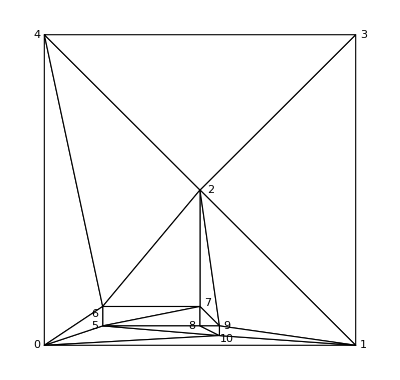

```mathematica
Show[
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[3]],q[[2]],q[[4]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[11]],q[[6]],q[[1]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[7]],q[[5]],q[[1]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[7]],q[[3]],q[[5]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[5]],q[[3]],q[[4]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[11]],q[[9]],q[[6]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[7]],q[[1]],q[[6]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[8]],q[[3]],q[[7]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[6]],q[[8]],q[[7]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[9]],q[[8]],q[[6]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[10]],q[[3]],q[[8]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[11]],q[[1]],q[[2]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[10]],q[[8]],q[[9]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[10]],q[[2]],q[[3]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[11]],q[[10]],q[[9]]}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{q[[11]],q[[2]],q[[10]]}]}],
Graphics[Text["0",q[[1]]+{-0.05,0.0}]],
Graphics[Text["1",q[[2]]+{0.05,0.0}]],
Graphics[Text["2",q[[3]]+{0.07,0.0}]],
Graphics[Text["3",q[[4]]+{0.05,0.0}]],
Graphics[Text["4",q[[5]]+{-0.05,0.0}]],
Graphics[Text["5",q[[6]]+{-0.05,0.0}]],
Graphics[Text["6",q[[7]]+{-0.05,-0.05}]],
Graphics[Text["7",q[[8]]+{0.05,0.02}]],
Graphics[Text["8",q[[9]]+{-0.05,0.0}]],
Graphics[Text["9",q[[10]]+{0.05,0.0}]],
Graphics[Text["10",q[[11]]+{0.05,-0.02}]]
]
```